```mathematica
ClearSystemCache[];
ClearAll["Global`*"];
<<NumericalDifferentialEquationAnalysis`
```

#### Optical properties

#### Matrix size

```mathematica
M=4;
```

#### Albedo

```mathematica
a=0.9;
```

#### Optical thickness

```mathematica
τ=1.0;
```

#### Anisotropy

```mathematica
g=0.9;
```

#### Refractive index

```mathematica
n=1.5;
nglass=1;
```

#### Quadrature angles

Total internal reflection

```mathematica
θ [n_]= ArcSin[1.0/n];
```

Critical cosine

```mathematica
νc[n_]=Cos[θ[n]];
```

Gauss (0<θ<ν_c)

```mathematica
gauss=GaussianQuadratureWeights[M/2,0,νc[n]];
νGauss=gauss[[All,1]];
wGauss=gauss[[All,2]];
```

Radau (ν_c<θ<1)

```mathematica
cachedLegendreP[k_,x_]:=cachedLegendreP[k,x]=LegendreP[k,x];
```

```mathematica
Radau[x_,m_]=(cachedLegendreP[m/2-1,x]+cachedLegendreP[m/2,x])/(1+x);
```

```mathematica
Der[x_,m_]=D[cachedLegendreP[m/2,x],x];
```

```mathematica
RadauRoots=Sort[Flatten[Chop[N[{x/.Solve[Radau[x,M]==0,x], -1}]]],Greater];
```

```mathematica
νRadau=Table[N[(1+νc[n])/2-(1-νc[n])/2×RadauRoots[[j]]],{j,M/2}];
```

```mathematica
wRadau=Flatten[{Table[(1-νc[n])/(2 (1-RadauRoots[[j]]) (Der[RadauRoots[[j]],M-2])^2),{j,M/2-1}],{(1-νc[n])/(M/2)^2}}];
```

#### Final quadrature angles and weights

```mathematica
ν=Flatten[{νGauss,νRadau}];
w = Flatten[{wGauss,wRadau}];
ClearAll[RadauRoots,GaussLRoots,νGauss,νRadau,wGauss,wRadau];
```

```mathematica
anglesRad=Table[ArcCos[ν[[i]]],{i,Length[ν]}];
anglesDeg=Table[(anglesRad[[i]] 180)/π,{i,Length[ν]}];
```

### The Redistribution Function

#### δ-M method

```mathematica
τs[A_,T_,G_]:=τs[A,T,G]=(1-A G^M)T
```

```mathematica
as[A_,G_]:=as[A,G]=A(1-G^M)/(1-A×G^M)
```

Optical thickness of starting layer: Δτ^*<ν_1 (min ν)

We want Δτ^*×2^n1=τ^*

```mathematica
n1[A_,T_,G_]:=n1[A,T,G]=Module[{myN},myN=0;While[myN<100000,If[τs[A,T,G]<Min[ν]×2^myN,Break[]];myN++];myN]
n1[a,τ,g]
```

2

```mathematica
Δτs[A_,T_,G_]:=Δτs[A,T,G]=τs[A,T,G]/2^n1[A,T,G];
```

```mathematica
Δτ[A_,T_,G_]:=Δτ[A,T,G]=Δτs[A,T,G]/(1-A×G^M);
```

#### Heyney-Greenstein phase function

```mathematica
SuperStar[χ][k_,G_]:=SuperStar[χ][k,G]=(G^k-G^M)/(1-G^M);
```

```mathematica
PPmatrix=ConstantArray[0.,{M, M}];
PPmatrix[[1,All]]=1.;
PPmatrix[[2,All]]=ν;
Do[Do[PPmatrix[[nn,j]]=((2nn-3) ν[[j]] PPmatrix[[nn-1,j]]-(nn-2) PPmatrix[[nn-2,j]])/(nn-1),{nn,3,M}],{j,M}];
PNmatrix=Table[(-1)^(nn-1) PPmatrix[[nn,j]],{nn,1,M},{j,1,M}];
```

```mathematica
(*hpp=ConstantArray[0.,{M, M}];
hpm=ConstantArray[0.,{M, M}];
If[g==0,
hpp=ConstantArray[1.,{M, M}];
hpm=ConstantArray[1.,{M, M}];
,
Do[Do[hpp[[i,j]]=Sum[(2k+1) χ^*[k]PPmatrix[[k+1,i]] PPmatrix[[k+1,j]],{k,0,M-1}],{j,i,M}],{i,M}];
Do[Do[hpp[[j,i]]=hpp[[i,j]],{j,i+1,M}],{i,M}];
Do[Do[hpm[[i,j]]=Sum[(2k+1) χ^*[k]PPmatrix[[k+1,i]] PNmatrix[[k+1,j]],{k,0,M-1}],{j,i,M}],{i,M}];
Do[Do[hpm[[j,i]]=hpm[[i,j]],{j,i+1,M}],{i,M}];
];*)
```

```mathematica
hpp[G_]:=hpp[G]=Module[{newHPP,i,j,k},newHPP=ConstantArray[0.,{M, M}];If[g==0,newHPP=ConstantArray[1.,{M, M}],Do[Do[newHPP[[i,j]]=Sum[(2k+1) SuperStar[χ][k,G]PPmatrix[[k+1,i]] PPmatrix[[k+1,j]],{k,0,M-1}],{j,i,M}],{i,M}];
Do[Do[newHPP[[j,i]]=newHPP[[i,j]],{j,i+1,M}],{i,M}]];newHPP];
hpm[G_]:=hpm[G]=Module[{newHPM,i,j,k},newHPM=ConstantArray[0.,{M, M}];If[g==0,newHPM=ConstantArray[1.,{M, M}],Do[Do[newHPM[[i,j]]=Sum[(2k+1) SuperStar[χ][k,G]PPmatrix[[k+1,i]] PNmatrix[[k+1,j]],{k,0,M-1}],{j,i,M}],{i,M}];
Do[Do[newHPM[[j,i]]=newHPM[[i,j]],{j,i+1,M}],{i,M}]];newHPM];
```

```mathematica
hpp[g]
```

{{1.60813,1.30369,0.663045,-0.0364742},{1.30369,1.94346,1.95748,1.73691},{0.663045,1.95748,3.15547,4.2362},{-0.0364742,1.73691,4.2362,6.84908}}

```mathematica
(*ClearAll[cachedLegendreP,PPmatrix,PNmatrix];*)
```

#### Layer Initialiation

```mathematica
EE=IdentityMatrix[M];
```

```mathematica
BB[A_,T_,G_]:=BB[A,T,G]=Table[(as[A,G]×Δτs[A,T,G]×w[[j]])/(4 ν[[i]]) hpm[G][[i,j]],{i,M},{j,M}];
```

```mathematica
AA[A_,T_,G_]:=AA[A,T,G]=Table[i,j Δτs[A,T,G]/(2 ν[[i]])-(as[A,G]×Δτs[A,T,G] w[[j]])/(4 ν[[i]])hpp[G][[i,j]],{i,M},{j,M}];
```

```mathematica
Inv[A_,T_,G_]:=Inv[A,T,G]=Inverse[EE+AA[A,T,G]];
```

```mathematica
GG[A_,T_,G_]:=GG[A,T,G]=Inverse[EE+AA[A,T,G]-BB[A,T,G].Inv[A,T,G].BB[A,T,G]];
```

```mathematica
RR[A_,T_,G_]:=RR[A,T,G]=2.GG[A,T,G].BB[A,T,G].Inv[A,T,G];
```

```mathematica
TT[A_,T_,G_]:=TT[A,T,G]=2.GG[A,T,G]-EE;
```

```mathematica
(*ClearAll[A,B,G,Inv,hpp,hpm];*)
```

```mathematica
twoaw=2 ν w;
```

```mathematica
Rd1[A_,T_,G_]:=Rd1[A,T,G]=Table[(RR[A,T,G][[i,j]])/twoaw[[j]],{i,M},{j,M}];
Td1[A_,T_,G_]:=Td1[A,T,G]=Table[(TT[A,T,G][[i,j]])/twoaw[[j]],{i,M},{j,M}];
```

#### Doubling until desired thickness is reached

```mathematica
newE=DiagonalMatrix[1./twoaw];
star=DiagonalMatrix[twoaw];
```

Now I’ll try to avoid recursion here...

```mathematica
Td2=ConstantArray[0.,{M,M}];
Rd2=ConstantArray[0.,{M,M}];
Td[A_,T_,G_]:=Td[A,T,G]=Table[Td1[A,T,G],{i,n1[A,T,G]+1}];
Rd[A_,T_,G_]:=Rd[A,T,G]=Table[Rd1[A,T,G],{i,n1[A,T,G]+1}];
```

```mathematica
makeTChain[A_,T_,G_]:=makeTChain[A,T,G]=Module[{i,Tchain,Rchain},Tchain=Table[Td1[A,T,G],{i,n1[A,T,G]+1}];Rchain=Table[Rd1[A,T,G],{i,n1[A,T,G]+1}];
For[i=1,i≤n1[A,T,G],i++,
Tchain[[i+1]]=Tchain[[i]].Inverse[newE-Rchain[[i]].star.Rchain[[i]]].Tchain[[i]];
Rchain[[i+1]]=Tchain[[i]].Inverse[newE-Rchain[[i]].star.Rchain[[i]]].Rchain[[i]].star.Tchain[[i]]+Rchain[[i]]
];Tchain];
makeRChain[A_,T_,G_]:=makeRChain[A,T,G]=Module[{i,Tchain,Rchain},Tchain=Table[Td1[A,T,G],{i,n1[A,T,G]+1}];Rchain=Table[Rd1[A,T,G],{i,n1[A,T,G]+1}];
For[i=1,i≤n1[A,T,G],i++,
Tchain[[i+1]]=Tchain[[i]].Inverse[newE-Rchain[[i]].star.Rchain[[i]]].Tchain[[i]];
Rchain[[i+1]]=Tchain[[i]].Inverse[newE-Rchain[[i]].star.Rchain[[i]]].Rchain[[i]].star.Tchain[[i]]+Rchain[[i]]
];Rchain];
```

```mathematica
(*For[i=1,i≤n1[A,T],i++,
Td[A,T][[i+1]]=Td[A,T][[i]].Inverse[newE-Rd[A,T][[i]].star.Rd[A,T][[i]]].Td[A,T][[i]];
Rd[A,T][[i+1]]=Td[A,T][[i]].Inverse[newE-Rd[A,T][[i]].star.Rd[A,T][[i]]].Rd[A,T][[i]].star.Td[A,T][[i]]+Rd[A,T][[i]]
];*)
```

R and T for desired optical thickness

```mathematica
Rslab[A_,T_,G_]:=Rslab[A,T,G]=makeRChain[A,T,G][[n1[A,T,G]+1]];
Tslab[A_,T_,G_]:=Tslab[A,T,G]=makeTChain[A,T,G][[n1[A,T,G]+1]];
```

#### Fresnel reflection & boundary conditions

```mathematica
νt[ni_,nt_,νi_]=√(1-(ni/nt)^2 (1-νi^2));
FresnelR[νi_,ni_,nt_]=1/2 ((nt νi-ni Re[νt[ni,nt,νi]])/(nt νi+ni Re[νt[ni,nt,νi]]))^2+1/2 ((ni νi-nt Re[νt[ni,nt,νi]])/(ni νi+nt Re[νt[ni,nt,νi]]))^2;
Rbound=DiagonalMatrix[Re[Chop[((FresnelR[ν,n,nglass]+FresnelR[νt[n,nglass,ν],nglass,1]-2×FresnelR[ν,n,nglass]×FresnelR[νt[n,nglass,ν],nglass,1])/(1-FresnelR[ν,n,nglass]×FresnelR[νt[n,nglass,ν],nglass,1]))× twoaw]]];
Tbound=DiagonalMatrix[Re[Chop[1-(FresnelR[ν,n,nglass]+FresnelR[νt[n,nglass,ν],nglass,1]-2×FresnelR[ν,n,nglass]×FresnelR[νt[n,nglass,ν],nglass,1])/(1-FresnelR[ν,n,nglass]×FresnelR[νt[n,nglass,ν],nglass,1])]]];
```

#### Adding boundaries to the slab

```mathematica
T02[A_,T_,G_]:=T02[A,T,G]=Tslab[A,T,G].Inverse[EE-Rbound.Rslab[A,T,G]].Tbound;
R20[A_,T_,G_]:=R20[A,T,G]=Tslab[A,T,G].Inverse[EE-Rbound.Rslab[A,T,G]].Rbound.Tslab[A,T,G]+Rslab[A,T,G];
```

```mathematica
T03[A_,T_,G_]:=T03[A,T,G]=Module[{newT03},newT03=ConstantArray[0,{M,M}];If[A==0||T==0,newT03=Re[Chop[Tbound.Inverse[EE].T02[A,T,G]]],newT03=Re[Chop[Tbound.Inverse[EE-R20[A,T,G].Rbound].T02[A,T,G]]]];newT03];
R30[A_,T_,G_]:=R30[A,T,G]=Module[{newR30},newR30=ConstantArray[0,{M,M}];If[A==0||T==0,newR30=Re[Chop[Tbound.Inverse[EE].R20[A,T,G].Tbound]],newR30=Re[Chop[Tbound.Inverse[EE-R20[A,T,G].Rbound].R20[A,T,G].Tbound]]];newR30];
```

```mathematica
modifyR30[A_,T_,G_]:=modifyR30[A,T,G]=Module[{newR30,i},newR30=R30[A,T,G];For[i=1,i≤M,i++,newR30[[i,i]]+=Rbound[[i,i]]/twoaw[[i]]^2];newR30];
```

```mathematica
(*For[i=1,i≤M,i++,R30[A,T][[i,i]]+=Rbound[[i,i]]/twoaw[[i]]^2];*)
```

```mathematica
Rc[A_,T_,G_]:=Rc[A,T,G]=Total[2 ν w×modifyR30[A,T,G][[M]]]
Tc[A_,T_,G_]:=Tc[A,T,G]=Total[2 ν w T03[A,T,G][[M]]]
```

```mathematica
{Rc[a,τ,g],Tc[a,τ,g]}
```

{0.0839645,0.753912}

```mathematica
Rm=0.1484895;
Tm=0.499587;
```

```mathematica
MM[A_,T_,G_]:=MM[A,T,G]=Abs[Rc[A,T,G]-Rm]/(Rm+10^-6)+Abs[Tc[A,T,G]-Tm]/(Tm+10^-6);
```

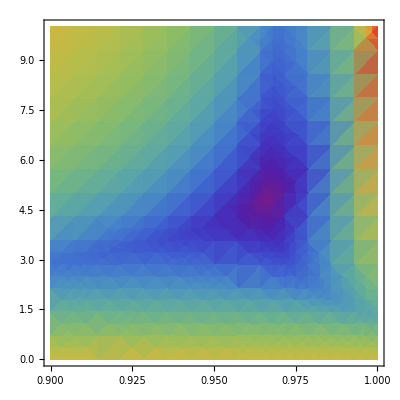

```mathematica
DensityPlot[MM[A,T,0.9],{A,0.9,1},{T,0,10},PlotRange->All,ColorFunction->"Rainbow"]
```